## QuantumSystems Documentation

## Preamble

```mathematica
Needs["QuantumSystems`"]
```

The following packages are needed to run some code found in this documentation notebook.

```mathematica
Needs["DocTools`"]
Needs["Visualization`"]
```

## Introduction and Overview

This package includes functions for:
• Constructing states and operators for quantum systems, including spin systems, cavity systems, qubits, qudits, and quantum circuits.
• Computing measures on quantum states, including Purity, Fidelity, entropic measures, P-norms, and some limited support for entanglement measures.
• Constructing random unitary matrices and random density matrices.

## States, Gates and Operators

### Spin Operators

Spin Operators
Spin[X][J] returns the matrix representation of the Spin-X operator with total spin value J.
Spin[Y][J] returns the matrix representation of the Spin-Y operator with total spin value J.
Spin[Z][J] returns the matrix representation of the Spin-Z operator with total spin value J.
Spin[P][J] returns the matrix representation of the Spin-Plus raising ladder operator with total spin value J.
Spin[M][J] returns the matrix representation of the Spin-Minus lowering ladder operator with total spin value J.
Spin[I][J] returns the IdentityMatrix of the same dimension as a spin operator with total spin value J.

Spin[n][J] returns the matrix representation of the Spin-n operator with total spin value J, where n=0,1,2, and 3 correspond to I,X,Y, and Z, respectively.

Multipartite Spin Operators
Spin[expr][J] may be used to construct multipartite spin operators using the TP parser from the Tensor package.
expr may consist of any string or symbols involving {I,X,Y,Z,P,M} and is evaluated as a tensor product where {I,X,Y,Z,P,M} are replaced with the corresponding Spin[op][J] matrix. 

Sparse Array Spin Operators
Spin[expr][J,SparseArray] returns the result of Spin[expr][J] as a SparseArray. 

Symbolic Spin Operators
Spin[expr] may be used to store a symbolic spin matrix and wont be evaluated until it is given an argument as Spin[expr][J].

#### Example 1

The spin 5/2 operator along Y.

```mathematica
Spin[Y][5/2]//MatrixForm
```

(0 | -(ⅈ √5)/2 | 0 | 0 | 0 | 0
(ⅈ √5)/2 | 0 | -ⅈ √2 | 0 | 0 | 0
0 | ⅈ √2 | 0 | -(3 ⅈ)/2 | 0 | 0
0 | 0 | (3 ⅈ)/2 | 0 | -ⅈ √2 | 0
0 | 0 | 0 | ⅈ √2 | 0 | -(ⅈ √5)/2
0 | 0 | 0 | 0 | (ⅈ √5)/2 | 0)

#### Example 2

Construct a secular dipolar Hamiltonian for two spin-1/2 particles

```mathematica
Spin[XX+YY-2ZZ][1/2]//MatrixForm
```

(-1/2 | 0 | 0 | 0
0 | 1/2 | 1/2 | 0
0 | 1/2 | 1/2 | 0
0 | 0 | 0 | -1/2)

#### Example 3

Construct a collective spin operator for 2 spin-1 particles

```mathematica
Spin[ZI+IZ][1]//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2)

#### Example 4

We can iterate over X,Y,Z using 1,2,3

```mathematica
Array[a[#]Spin[#][1]&,3]//MatrixListForm
```

(0 | a[1]/(√2) | 0
a[1]/(√2) | 0 | a[1]/(√2)
0 | a[1]/(√2) | 0),(0 | -(ⅈ a[2])/(√2) | 0
(ⅈ a[2])/(√2) | 0 | -(ⅈ a[2])/(√2)
0 | (ⅈ a[2])/(√2) | 0),(a[3] | 0 | 0
0 | 0 | 0
0 | 0 | -a[3])

Beware of confusing behaviour when putting local symbols (like n below) into the argument of Spin; this is due to the combination of the HoldAllComplete attribute of Spin and the way Table is implemented.

```mathematica
Table[With[{nn=n},a[n]Spin[n][1]],{n,3}]//MatrixListForm
```

a[1],2 a[2],3 a[3]

The simplest way to solve this is by using With injection:

```mathematica
Table[With[{nn=n},a[n]Spin[nn][1]],{n,3}]//MatrixListForm
```

(0 | a[1]/(√2) | 0
a[1]/(√2) | 0 | a[1]/(√2)
0 | a[1]/(√2) | 0),(0 | -(ⅈ a[2])/(√2) | 0
(ⅈ a[2])/(√2) | 0 | -(ⅈ a[2])/(√2)
0 | (ⅈ a[2])/(√2) | 0),(a[3] | 0 | 0
0 | 0 | 0
0 | 0 | -a[3])

### Cavity Operators

Cavity Operators
Cavity[a][m] returns the matrix representation of the annihilation operator for a cavity truncated to dimension m.
Cavity[c][m] returns the matrix representation of the creation operator a† for a cavity truncated to dimension m.
Cavity[n][m] returns the matrix representation of the number operator N=a†.a for a cavity truncated to dimension m.
Cavity[I][m] returns the IdentityMatrix for a cavity truncated to dimension m.

Multipartite Cavity Operators
Cavity[expr][m] may be used to construct multipartite cavity operators using the TP parser from the Tensor package.
expr may consist of any string or symbols involving {I,a,c,n} and is evaluated as a tensor product where
{I,a,c,n} are replaced with the corresponding Cavity[op][m] matrix. 

Sparse Array Cavity Operators
Cavity[expr][m,SparseArray] returns the result of Cavity[expr][m] as a SparseArray. 

Symbolic Cavity Operators
Cavity[expr] may be used to store a symbolic cavity matrix and wont be evaluated until it is given an argument as Cavity[expr][m].

#### Example 1

Construct a Jaynes cummings Hamiltonian for a 5 level truncated cavity

```mathematica
Spin[P][1/2]⊗Cavity[a][5]+Spin[M][1/2]⊗Cavity[c][5]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | √2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0)

#### Example 2

Construct a Tavis-cummings Hamiltonian for 3 spin-1/2 particles and a 5 level truncated cavity

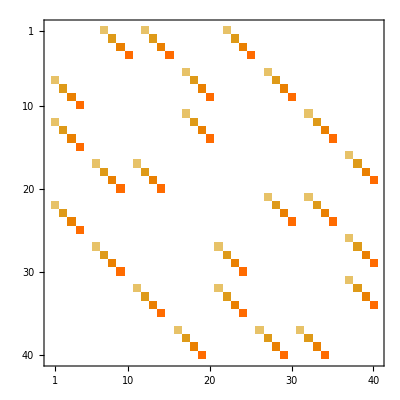

```mathematica
Spin[PII+IPI+IIP][1/2]⊗Cavity[a][5]+Spin[MII+IMI+IIM][1/2]⊗Cavity[c][5]//MatrixPlot
```

### QExpand

QExpand[expr] expands out symbolic forms of Spin and Cavity in expr. For example Spin[“λXX”] will be expanded to λ Spin[“X”]⊗Spin[“X”]. Expanded symbolic forms may be converted to matrices by using VecForm.

#### Example

Expanding symbolic spin operators

```mathematica
op=QExpand[Spin["PM+MP"]]
```

S_-⊗S_++S_+⊗S_-

The full form of this operator is

```mathematica
op//FullForm
```

Plus[CircleTimes[Spin["M"],Spin["P"]],CircleTimes[Spin["P"],Spin["M"]]]

We may convert back to a matrix for J=1/2 spins using VecForm

```mathematica
VecForm[op]
```

{{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,0}}

.. Or for J=1 instead

```mathematica
VecForm[op,Spin->1]
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,2,0,0,0,0,0},{0,0,0,0,2,0,0,0,0},{0,2,0,0,0,0,0,0,0},{0,0,2,0,0,0,2,0,0},{0,0,0,0,0,0,0,2,0},{0,0,0,0,2,0,0,0,0},{0,0,0,0,0,2,0,0,0},{0,0,0,0,0,0,0,0,0}}

### Quantum States

Qubits Density Matrices
QState[Zp],QState[H] return the density matrix for the qubit state |0⟩⟨0|.
QState[Zm],QState[V] return the density matrix for the qubit state |1⟩⟨1|.
QState[Xp],QState[D] return the density matrix for the qubit state |+⟩⟨+|.
QState[Xm],QState[A] return the density matrix for the qubit state |-⟩⟨-|.
QState[Yp],QState[R] return the density matrix for the qubit state |+i⟩⟨+i|.
QState[Ym],QState[L] return the density matrix for the qubit state |-i⟩⟨-i|.
QState[I] returns the density matrix for the maximally mixed qubit state.

Qubits States from Bloch Vectors
QState[{x1,y1,z1},{x2,y2,z2},...] returns the density matrix formed from the tensor product of qubit states with Bloch vectors {xj,yj,zj}.

2-Qubit Bell States
QState[Bell1],QState[B1] return the density matrix for 2-qubit Bell state (|00⟩+|11⟩)(⟨00|+⟨11|)/2.
QState[Bell2],QState[B2] return the density matrix for 2-qubit Bell state (|01⟩+|10⟩)(⟨01|+⟨10|)/2.
QState[Bell3],QState[B3] return the density matrix for 2-qubit Bell state (|01⟩-|10⟩)(⟨01|-⟨10|)/2.
QState[Bell4],QState[B4] return the density matrix for 2-qubit Bell state (|00⟩-|11⟩)(⟨00|-⟨11|)/2.

Options
QState[expr,VectorQ→True] returns the state QState[expr] as a state vector rather than a density matrix.
QState[expr,ColumnVectorQ→True] returns the state QState[expr] as a state vector ({d,1} dimensional column-vector) rather than a density matrix.

Multipartite States
QState[expr] returns the density matrix for the tensor product of states formed from the TP parser of expr where terms are replaced by the corresponding quantum states.

#### Options

Option | Default Value | Description
VectorQ | False | If set to True returns the resulting quantum state as a pure state vector.
ColumnVectorQ | False | If set to True returns the resulting state as a pure state column vector.

#### Example 1

Constructing 3-qubit GHZ and W states.

```mathematica
QState[HHH+VVV,VectorQ->True]/Sqrt[2]
%//KetForm
```

{1/(√2),0,0,0,0,0,0,1/(√2)}

(0_2,0_2,0_2)/(√2)+(1_2,1_2,1_2)/(√2)

```mathematica
QState[HHV+HVH+VHH,VectorQ->True]/√3
%//KetForm
```

{0,1/(√3),1/(√3),0,1/(√3),0,0,0}

(0_2,0_2,1_2)/(√3)+(0_2,1_2,0_2)/(√3)+(1_2,0_2,0_2)/(√3)

### Bra-Ket Notation

KetForm[op,{d1,d2,...,dn}] converts op into Bra-Ket notation, where op is a multipartite vector, or matrix with n-subsystems each of dimension dj.

KetForm[op,d] converts op into Bra-Ket notation, where op is a multipartite vector, or matrix where each subsystem has the same dimension d.

KetForm[op] converts op into Bra-Ket notation. If op is a multipartite vector or matrix where all subsystems are 2-dimensional, or all subsystems are 3-dimensional it will correctely express it in terms of subsystem bases, otherwise it will return it as a signle d-dimensional system.

#### Example

Converting a 3 qubit array into Bra-Ket notaiton

```mathematica
Array[a,{8,8}]//KetForm
```

a[1,1] |0_2 0_2 0_2⟩⟨0_2 0_2 0_2|+a[1,2] |0_2 0_2 0_2⟩⟨0_2 0_2 1_2|+a[1,3] |0_2 0_2 0_2⟩⟨0_2 1_2 0_2|+a[1,4] |0_2 0_2 0_2⟩⟨0_2 1_2 1_2|+a[1,5] |0_2 0_2 0_2⟩⟨1_2 0_2 0_2|+a[1,6] |0_2 0_2 0_2⟩⟨1_2 0_2 1_2|+a[1,7] |0_2 0_2 0_2⟩⟨1_2 1_2 0_2|+a[1,8] |0_2 0_2 0_2⟩⟨1_2 1_2 1_2|+a[2,1] |0_2 0_2 1_2⟩⟨0_2 0_2 0_2|+a[2,2] |0_2 0_2 1_2⟩⟨0_2 0_2 1_2|+a[2,3] |0_2 0_2 1_2⟩⟨0_2 1_2 0_2|+a[2,4] |0_2 0_2 1_2⟩⟨0_2 1_2 1_2|+a[2,5] |0_2 0_2 1_2⟩⟨1_2 0_2 0_2|+a[2,6] |0_2 0_2 1_2⟩⟨1_2 0_2 1_2|+a[2,7] |0_2 0_2 1_2⟩⟨1_2 1_2 0_2|+a[2,8] |0_2 0_2 1_2⟩⟨1_2 1_2 1_2|+a[3,1] |0_2 1_2 0_2⟩⟨0_2 0_2 0_2|+a[3,2] |0_2 1_2 0_2⟩⟨0_2 0_2 1_2|+a[3,3] |0_2 1_2 0_2⟩⟨0_2 1_2 0_2|+a[3,4] |0_2 1_2 0_2⟩⟨0_2 1_2 1_2|+a[3,5] |0_2 1_2 0_2⟩⟨1_2 0_2 0_2|+a[3,6] |0_2 1_2 0_2⟩⟨1_2 0_2 1_2|+a[3,7] |0_2 1_2 0_2⟩⟨1_2 1_2 0_2|+a[3,8] |0_2 1_2 0_2⟩⟨1_2 1_2 1_2|+a[4,1] |0_2 1_2 1_2⟩⟨0_2 0_2 0_2|+a[4,2] |0_2 1_2 1_2⟩⟨0_2 0_2 1_2|+a[4,3] |0_2 1_2 1_2⟩⟨0_2 1_2 0_2|+a[4,4] |0_2 1_2 1_2⟩⟨0_2 1_2 1_2|+a[4,5] |0_2 1_2 1_2⟩⟨1_2 0_2 0_2|+a[4,6] |0_2 1_2 1_2⟩⟨1_2 0_2 1_2|+a[4,7] |0_2 1_2 1_2⟩⟨1_2 1_2 0_2|+a[4,8] |0_2 1_2 1_2⟩⟨1_2 1_2 1_2|+a[5,1] |1_2 0_2 0_2⟩⟨0_2 0_2 0_2|+a[5,2] |1_2 0_2 0_2⟩⟨0_2 0_2 1_2|+a[5,3] |1_2 0_2 0_2⟩⟨0_2 1_2 0_2|+a[5,4] |1_2 0_2 0_2⟩⟨0_2 1_2 1_2|+a[5,5] |1_2 0_2 0_2⟩⟨1_2 0_2 0_2|+a[5,6] |1_2 0_2 0_2⟩⟨1_2 0_2 1_2|+a[5,7] |1_2 0_2 0_2⟩⟨1_2 1_2 0_2|+a[5,8] |1_2 0_2 0_2⟩⟨1_2 1_2 1_2|+a[6,1] |1_2 0_2 1_2⟩⟨0_2 0_2 0_2|+a[6,2] |1_2 0_2 1_2⟩⟨0_2 0_2 1_2|+a[6,3] |1_2 0_2 1_2⟩⟨0_2 1_2 0_2|+a[6,4] |1_2 0_2 1_2⟩⟨0_2 1_2 1_2|+a[6,5] |1_2 0_2 1_2⟩⟨1_2 0_2 0_2|+a[6,6] |1_2 0_2 1_2⟩⟨1_2 0_2 1_2|+a[6,7] |1_2 0_2 1_2⟩⟨1_2 1_2 0_2|+a[6,8] |1_2 0_2 1_2⟩⟨1_2 1_2 1_2|+a[7,1] |1_2 1_2 0_2⟩⟨0_2 0_2 0_2|+a[7,2] |1_2 1_2 0_2⟩⟨0_2 0_2 1_2|+a[7,3] |1_2 1_2 0_2⟩⟨0_2 1_2 0_2|+a[7,4] |1_2 1_2 0_2⟩⟨0_2 1_2 1_2|+a[7,5] |1_2 1_2 0_2⟩⟨1_2 0_2 0_2|+a[7,6] |1_2 1_2 0_2⟩⟨1_2 0_2 1_2|+a[7,7] |1_2 1_2 0_2⟩⟨1_2 1_2 0_2|+a[7,8] |1_2 1_2 0_2⟩⟨1_2 1_2 1_2|+a[8,1] |1_2 1_2 1_2⟩⟨0_2 0_2 0_2|+a[8,2] |1_2 1_2 1_2⟩⟨0_2 0_2 1_2|+a[8,3] |1_2 1_2 1_2⟩⟨0_2 1_2 0_2|+a[8,4] |1_2 1_2 1_2⟩⟨0_2 1_2 1_2|+a[8,5] |1_2 1_2 1_2⟩⟨1_2 0_2 0_2|+a[8,6] |1_2 1_2 1_2⟩⟨1_2 0_2 1_2|+a[8,7] |1_2 1_2 1_2⟩⟨1_2 1_2 0_2|+a[8,8] |1_2 1_2 1_2⟩⟨1_2 1_2 1_2|

Converting the same array as a 4-dimensional and 2-dimensional system

```mathematica
KetForm[Array[a,{8,8}],{4,2}]
```

a[1,1] |0_4 0_2⟩⟨0_4 0_2|+a[1,2] |0_4 0_2⟩⟨0_4 1_2|+a[1,3] |0_4 0_2⟩⟨1_4 0_2|+a[1,4] |0_4 0_2⟩⟨1_4 1_2|+a[1,5] |0_4 0_2⟩⟨2_4 0_2|+a[1,6] |0_4 0_2⟩⟨2_4 1_2|+a[1,7] |0_4 0_2⟩⟨3_4 0_2|+a[1,8] |0_4 0_2⟩⟨3_4 1_2|+a[2,1] |0_4 1_2⟩⟨0_4 0_2|+a[2,2] |0_4 1_2⟩⟨0_4 1_2|+a[2,3] |0_4 1_2⟩⟨1_4 0_2|+a[2,4] |0_4 1_2⟩⟨1_4 1_2|+a[2,5] |0_4 1_2⟩⟨2_4 0_2|+a[2,6] |0_4 1_2⟩⟨2_4 1_2|+a[2,7] |0_4 1_2⟩⟨3_4 0_2|+a[2,8] |0_4 1_2⟩⟨3_4 1_2|+a[3,1] |1_4 0_2⟩⟨0_4 0_2|+a[3,2] |1_4 0_2⟩⟨0_4 1_2|+a[3,3] |1_4 0_2⟩⟨1_4 0_2|+a[3,4] |1_4 0_2⟩⟨1_4 1_2|+a[3,5] |1_4 0_2⟩⟨2_4 0_2|+a[3,6] |1_4 0_2⟩⟨2_4 1_2|+a[3,7] |1_4 0_2⟩⟨3_4 0_2|+a[3,8] |1_4 0_2⟩⟨3_4 1_2|+a[4,1] |1_4 1_2⟩⟨0_4 0_2|+a[4,2] |1_4 1_2⟩⟨0_4 1_2|+a[4,3] |1_4 1_2⟩⟨1_4 0_2|+a[4,4] |1_4 1_2⟩⟨1_4 1_2|+a[4,5] |1_4 1_2⟩⟨2_4 0_2|+a[4,6] |1_4 1_2⟩⟨2_4 1_2|+a[4,7] |1_4 1_2⟩⟨3_4 0_2|+a[4,8] |1_4 1_2⟩⟨3_4 1_2|+a[5,1] |2_4 0_2⟩⟨0_4 0_2|+a[5,2] |2_4 0_2⟩⟨0_4 1_2|+a[5,3] |2_4 0_2⟩⟨1_4 0_2|+a[5,4] |2_4 0_2⟩⟨1_4 1_2|+a[5,5] |2_4 0_2⟩⟨2_4 0_2|+a[5,6] |2_4 0_2⟩⟨2_4 1_2|+a[5,7] |2_4 0_2⟩⟨3_4 0_2|+a[5,8] |2_4 0_2⟩⟨3_4 1_2|+a[6,1] |2_4 1_2⟩⟨0_4 0_2|+a[6,2] |2_4 1_2⟩⟨0_4 1_2|+a[6,3] |2_4 1_2⟩⟨1_4 0_2|+a[6,4] |2_4 1_2⟩⟨1_4 1_2|+a[6,5] |2_4 1_2⟩⟨2_4 0_2|+a[6,6] |2_4 1_2⟩⟨2_4 1_2|+a[6,7] |2_4 1_2⟩⟨3_4 0_2|+a[6,8] |2_4 1_2⟩⟨3_4 1_2|+a[7,1] |3_4 0_2⟩⟨0_4 0_2|+a[7,2] |3_4 0_2⟩⟨0_4 1_2|+a[7,3] |3_4 0_2⟩⟨1_4 0_2|+a[7,4] |3_4 0_2⟩⟨1_4 1_2|+a[7,5] |3_4 0_2⟩⟨2_4 0_2|+a[7,6] |3_4 0_2⟩⟨2_4 1_2|+a[7,7] |3_4 0_2⟩⟨3_4 0_2|+a[7,8] |3_4 0_2⟩⟨3_4 1_2|+a[8,1] |3_4 1_2⟩⟨0_4 0_2|+a[8,2] |3_4 1_2⟩⟨0_4 1_2|+a[8,3] |3_4 1_2⟩⟨1_4 0_2|+a[8,4] |3_4 1_2⟩⟨1_4 1_2|+a[8,5] |3_4 1_2⟩⟨2_4 0_2|+a[8,6] |3_4 1_2⟩⟨2_4 1_2|+a[8,7] |3_4 1_2⟩⟨3_4 0_2|+a[8,8] |3_4 1_2⟩⟨3_4 1_2|

Or as a single 8-dimensional system

```mathematica
KetForm[Array[a,{8,8}],8]
```

a[1,1] |0_8⟩⟨0_8|+a[1,2] |0_8⟩⟨1_8|+a[1,3] |0_8⟩⟨2_8|+a[1,4] |0_8⟩⟨3_8|+a[1,5] |0_8⟩⟨4_8|+a[1,6] |0_8⟩⟨5_8|+a[1,7] |0_8⟩⟨6_8|+a[1,8] |0_8⟩⟨7_8|+a[2,1] |1_8⟩⟨0_8|+a[2,2] |1_8⟩⟨1_8|+a[2,3] |1_8⟩⟨2_8|+a[2,4] |1_8⟩⟨3_8|+a[2,5] |1_8⟩⟨4_8|+a[2,6] |1_8⟩⟨5_8|+a[2,7] |1_8⟩⟨6_8|+a[2,8] |1_8⟩⟨7_8|+a[3,1] |2_8⟩⟨0_8|+a[3,2] |2_8⟩⟨1_8|+a[3,3] |2_8⟩⟨2_8|+a[3,4] |2_8⟩⟨3_8|+a[3,5] |2_8⟩⟨4_8|+a[3,6] |2_8⟩⟨5_8|+a[3,7] |2_8⟩⟨6_8|+a[3,8] |2_8⟩⟨7_8|+a[4,1] |3_8⟩⟨0_8|+a[4,2] |3_8⟩⟨1_8|+a[4,3] |3_8⟩⟨2_8|+a[4,4] |3_8⟩⟨3_8|+a[4,5] |3_8⟩⟨4_8|+a[4,6] |3_8⟩⟨5_8|+a[4,7] |3_8⟩⟨6_8|+a[4,8] |3_8⟩⟨7_8|+a[5,1] |4_8⟩⟨0_8|+a[5,2] |4_8⟩⟨1_8|+a[5,3] |4_8⟩⟨2_8|+a[5,4] |4_8⟩⟨3_8|+a[5,5] |4_8⟩⟨4_8|+a[5,6] |4_8⟩⟨5_8|+a[5,7] |4_8⟩⟨6_8|+a[5,8] |4_8⟩⟨7_8|+a[6,1] |5_8⟩⟨0_8|+a[6,2] |5_8⟩⟨1_8|+a[6,3] |5_8⟩⟨2_8|+a[6,4] |5_8⟩⟨3_8|+a[6,5] |5_8⟩⟨4_8|+a[6,6] |5_8⟩⟨5_8|+a[6,7] |5_8⟩⟨6_8|+a[6,8] |5_8⟩⟨7_8|+a[7,1] |6_8⟩⟨0_8|+a[7,2] |6_8⟩⟨1_8|+a[7,3] |6_8⟩⟨2_8|+a[7,4] |6_8⟩⟨3_8|+a[7,5] |6_8⟩⟨4_8|+a[7,6] |6_8⟩⟨5_8|+a[7,7] |6_8⟩⟨6_8|+a[7,8] |6_8⟩⟨7_8|+a[8,1] |7_8⟩⟨0_8|+a[8,2] |7_8⟩⟨1_8|+a[8,3] |7_8⟩⟨2_8|+a[8,4] |7_8⟩⟨3_8|+a[8,5] |7_8⟩⟨4_8|+a[8,6] |7_8⟩⟨5_8|+a[8,7] |7_8⟩⟨6_8|+a[8,8] |7_8⟩⟨7_8|

### VecForm

VecForm[expr, opts] converts an symbolic expression with terms Ket, Bra, BraKet, KetBra, Spin and Cavity into a matrix or vector. If expr is a already a matrix it returns expr.

Options
• SparseArray→True specifies that the resulting matrix should be returned as a SparseArray. The default value is False which returns a normal matrix.
• Spin→J specifies the total spin-value to be used when converting Spin operators to matrices. The default value is 1/2.
• Cavity→n specifies the truncated cavity dimension to be used when converting Cavity operators to matrices. The default value is 2.

#### Example

Constructing a 4-qubit cat state

```mathematica
(Ket[0,0,0,0]+Ket[1,1,1,1])/Sqrt[2]
VecForm[%]
```

(0,0,0,0+1,1,1,1)/(√2)

{{1/(√2)},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1/(√2)}}

### Controlled Gates

Single Controlled Gate
CGate[{d1,...,dn},U,targ,ctrl,opts] returns the unitary matrix for the controlled gate U acting on subsystem targ which is activated by state |1⟩  on subsystem ctrl, and applies the IdentityMatrix for all other values |j≠1⟩ on subsystem ctrl, where {d1,...,dn} are the dimensions of all subsystems.

CGate[d,U,targ,ctrl,opts] assumes that the number of subsystems is given by the largest value of targ or ctrl, and that each subsystem has dimension d.

CGate[U,targ,ctrl,opts] assumes that each subsystem has the same dimension as the gate U.

Multiple Controlled Gates
CGate[dims,{U1,...,Un},{t1,...,tn},{c1,...,ck},opts] returns a unitary matrix for the controlled gate where multiple gates {U1,...,Un} are triggered on subsytems {t1,...,tn}, for specific control string of multiple control subsystems {c1,...,ck}.

Options
• Control→val specifies the basis state |val⟩ of the target system to apply the gate U on, where val∈{0,...,d-1}. The default value is 1.
• Control→{v1,...,vk}allows for specifying seperate control values for each control subsystem in the multiple gate case.

#### Options

```mathematica
DisplayOptions[CGate]
```

Option | Default Value | Description
Control | 1 | Specifies the state of the control subsystem to trigger the into controlled gate. Value may range from 0 to d-1 for a d-dimensional system. The value may also be a list of control values for a gate with multiple control subsystems.

#### Examples 1

Construct a CNOT gate

```mathematica
CGate[TP[X],2,1]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

Construct a Toffoli Gate

```mathematica
CGate[TP[X],3,{1,2}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

## State Measures

### Entropic Measures

EntropyH[{p1,...,pn}] yields the base-2 Shannon entropy of the discrete distribution with probabilities {p1,...,pn}.

EntropyS[mat] yields von-Neumann entropy of a density matrix mat.

RelativeEntropyS[mat1,mat2] yields the relative entropy S(mat1||mat2) for two density matrices mat1,mat2.

MutualInformationS[mat,{d1,d2}] calculates the mutual information of the bipartite density matrix mat with subsystem dimensions d1 and d2.

MutualInformationS[mat] assumes that subsystems have equal dimension.

#### Example 1

Shannon Entropy and Von-Neuman entropy for a diagonal matrix are equivalent:

```mathematica
EntropyH[{3/4,1/4}]
%//N
```

1/2+(3 Log[4/3])/(4 Log[2])

0.811278

```mathematica
EntropyS[DiagonalMatrix[{3/4,1/4}]]
%//N
```

1/2+(3 Log[4/3])/(4 Log[2])

0.811278

#### Example 2

Relative entropy may evaluate to infinity if the second state is singular:

```mathematica
RelativeEntropyS[QState[Zp],QState[Zm]]
```

∞

```mathematica
RelativeEntropyS[QState[Zp],QState[{0,0,3/4}]]
```

Log[8/7]/Log[2]

#### Example 3

```mathematica
MutualInformationS[QState[Bell1]]
```

2

```mathematica
MutualInformationS[QState[ZpXp]]
```

0

### Purity

Purity[mat] calculates the purity Tr[mat†.mat] of a density matrix mat.

Purity[mat,Normalize→True] rescales the Purity of the density matrix mat to be value between 0 and 1, rather than 1/d and 1.

#### Example

Purity of a qubit in terms of its Bloch vector

```mathematica
FullSimplify[Purity[QState[{a,b,c}]],{a,b,c}∈Reals]
```

1/2 (1+a^2+b^2+c^2)

### P-Norms

PNorm[op,p] computes the p-norm of a matrix or vector op where p=1,2,...∞. If no value of p is specified it defaults to p=∞ for matrixs, and p=2 for vectors.

#### Example

Calculate the trace distance between two quantum states:

```mathematica
PNorm[QState[Zp]-QState[Xm],1]
```

√2

### Fidelity

Fidelity[op1,op2] returns the fidelity of two quantum states op1, op2 which may be either state vectors or density matrices. The convention used is F=||√op1.√op2(||)_1=Tr √(√op1.op2.√op1).

#### Example

```mathematica
Fidelity[QState[Zp],QState[Xp]]
```

1/(√2)

### Entanglement Measures

EntangledQ[mat,{d1,d2}] returns True if the bipartite state mat with subsystems of dimensions d1 and d2 is entangled as determined by the Positive Partial Transpose test, and returns False or “Indeterminate” otherwise. The PPT is only sufficient for determining False if the two systems are both qubits, or a qubit and a qutrit.

EntangledQ[mat,{d1,d2},fun] applies the pure function fun to the eigenvalues of the PPT of mat and can be used to simplify the expression of input any assumptions.

EntangledQ[mat] and EntangledQ[mat,fun] assume that both subsystems have the same dimension.

Concurrence[op] computes the concurrence entanglement measure for a 2-qubit density matrix or state vector op.

EntanglementF[op] computes the entanglement of formation entanglement measure for a 2-qubit density matrix or state vector op.

#### Example 1

Concurrence and Entanglement of formation for the a state √p 0,0+√(1-p)0,0:

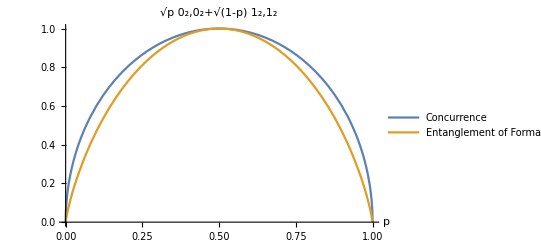

```mathematica
Plot[{Concurrence[{√p,0,0,√(1-p)}],EntanglementF[{√p,0,0,√(1-p)}]},{p,0,1},PlotLegends->{"Concurrence","Entanglement of Formation"},AxesLabel->{"p"},PlotLabel->KetForm[{√p,0,0,√(1-p)}]]
```

#### Example 2

Test to see if a state is entangled:

```mathematica
EntangledQ[QState[Bell1]]
```

True

Test a mixture of two orthogonal Bell states:

```mathematica
entq=EntangledQ[p*QState[Bell1]+(1-p)*QState[Bell4],FullSimplify[#,0≤p≤1]&]
```

If[Negative[1/2-p]||Negative[-1/2+p],True,If[Length[{{(1-p)/2+p/2,0,0,1/2 (-1+p)+p/2},{0,0,0,0},{0,0,0,0},{1/2 (-1+p)+p/2,0,0,(1-p)/2+p/2}}]≤6,False,Indeterminate]]

```mathematica
Table[{"p="<>ToString[p],entq},{p,0,1,0.1}]//MatrixForm
```

(p=0. | True
p=0.1 | True
p=0.2 | True
p=0.3 | True
p=0.4 | True
p=0.5 | False
p=0.6 | True
p=0.7 | True
p=0.8 | True
p=0.9 | True
p=1. | True)

## Random States and Operators

### Random Unitary

RandomUnitary[d] generates a pseudo-random {d,d} dimensional Unitary matrix that is (supposedly) uniform over the Haar measure.

#### Example

Test an approximate Unitary 2 design

```mathematica
u2design={#,Mean[Table[Conjugate[#]⊗#&@RandomUnitary[2],{#}]]}&/@{10,10^2,10^3,10^4,10^5};
```

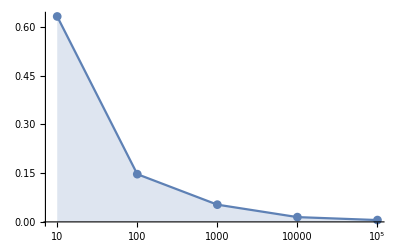

```mathematica
ListLogLinearPlot[{First[#],Norm[QState[Bell1]-Last[#],1]}&/@u2design,Joined->True,PlotMarkers->Automatic,Filling->Axis]
```

### Random Density Matrix

RandomDensity[d] generates a pesudo-random {d,d} dimensional density matrix that is uniformly distributed with respect to the Hilbert-Schmidt norm.

RandomDensity[d,r] generates a rank-r pseudo-random {d,d} dimensional density matrix that is uniformly distributed with respect to the Hilbert-Schmidt norm.

RandomDensity[d,”Bures”] and RandomDensity[d,r,”Bures”] generates a  the pesudo-random density matrix that is uniformly distributed with respect to the Bures measure.

#### Example

Eigenvalues of random states

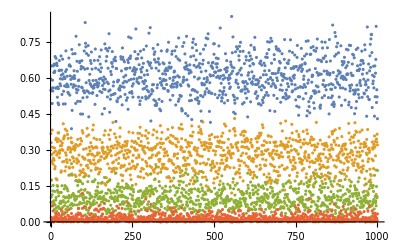

```mathematica
states=Transpose@Table[Eigenvalues[RandomDensity[4]],{1000}];
ListPlot[states]
```

and again using the Bures measure

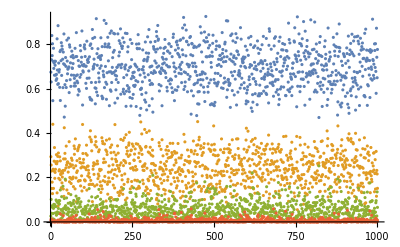

```mathematica
statesBures=Transpose@Table[Eigenvalues[RandomDensity[4,"Bures"]],{1000}];
ListPlot[statesBures]
```

```mathematica
states=Transpose@Table[Eigenvalues[RandomDensity[4]],{1000}];
```

### Random Hermitian Matrix

RandomHermitian[d] generates a psuedo-random {d,d} dimensiona Hermitian matrix with unit 1-norm.